# Inverse Transform Method

## Example 1: Triangular Distribution

## SCIMATH202 Project: Spring 2021 University College Roosevelt Robin van den Berg

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
(* This line clears all variables previously defined by the user. *)
```

```mathematica
n=50000;
(* This defines our sample size for the simulation (N). *)
```

```mathematica
f[x_]:=Piecewise[{{x+1,-1≤x<0},{1-x,0≤x≤1},{0,x<-1||x>1}}];
(* This defines the distribution f(x) from which we want to sample. *)
```

```mathematica
Finv1[x_]:=√(2x)-1;
Finv2[x_]:=1-√(2-2x);
(* This defines the inverse of the CDF that we caclulated in the project report. *)
```

```mathematica
U=RandomVariate[UniformDistribution[{0,1}],{n}];
(* This generates a random sample of size n from the unfiform distribution between 0 and 1. *)
```

```mathematica
data=Map[If[#≥1/2,Finv2[#],Finv1[#]]&,U];
(* This transform our sample from the Uniform distribution into a sample from the Triangular distribution. *)
```

```mathematica
plotdata=Flatten[data,1];
(* This alters the format of the table so that it is suitable for graphing. It stores this newly formatted table as a new variable. *)
```

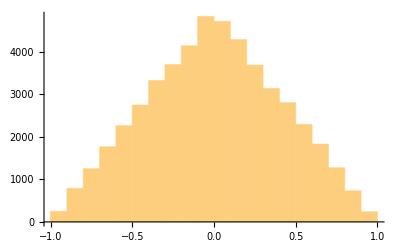

```mathematica
Histogram[plotdata]
```

```mathematica
p1=Histogram[plotdata,{-2,2,0.1},"Probability"];
p2=Plot[0.1f[x],{x,-2,2}];
(* This plots the transfromed Subscript[x, i] against the pdf f(x) to ensure that the transformed Subscript[x, i] follow the desired distribution. *)
```

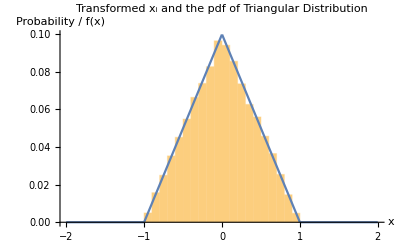

```mathematica
Show[p1,p2, PlotLabel-> "Transformed x_i and the pdf of Triangular Distribution",AxesLabel->{"x","Probability / f(x) "}]
```